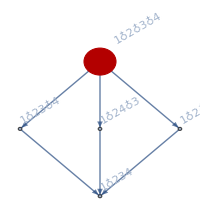
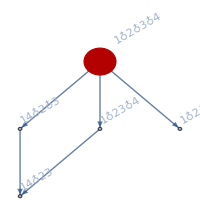
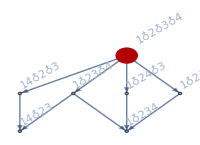
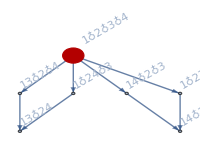
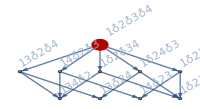
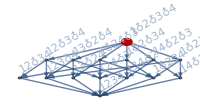
2→{{-Graphics-,62}}
3→{{-Graphics-,90}}
4→{{-Graphics-,16},{-Graphics-,12}}
5→{{-Graphics-,50},{-Graphics-,60}}
6→{}
7→{{-Graphics-,84},{-Graphics-,21}}
8→{}
9→{}
10→{{-Graphics-,60}}
11→{}
12→{}
13→{}
14→{}
15→{{-Graphics-,15}}

```mathematica
With[{all=allGraphs4,allKeys=allGraphs4AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,15}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

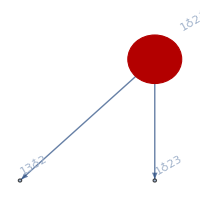
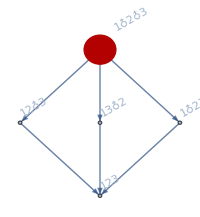
2→{{-Graphics-,12}}
3→{{-Graphics-,9}}
4→{}
5→{{-Graphics-,5}}

```mathematica
With[{all=allGraphs3,allKeys=allGraphs3AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,5}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

```mathematica
With[{all=allGraphs2,allKeys=allGraphs2AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,5}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

2→{{-Graphics-,2}}
3→{}
4→{}
5→{}

```mathematica
With[{all=allGraphs6,allKeys=allGraphs6AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[{Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200],PlanarGraphQ[all[#,"graph"]]}&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,2}], TableDirections->Column, TableDepth->1],{n,k}]
]
```